```mathematica
L=4*2.2;
h=0.41;
μ=0.001;
```

```mathematica
(*height profile of the manifold*)
```

```mathematica
z[y_]:=(2)y(h-y)/h^2 (y-h/24) /h
```

```mathematica
(*sg = Sqrt[Det[g_{ij}]]*)
```

```mathematica
sg[y_]:=Sqrt[1+(z'[y])^2]
```

```mathematica
B=Δ/μ*NIntegrate[sg[v]sg[u] If[u<=v,1,0],{u,0,h},{v,0,h}]/NIntegrate[sg[u],{u,0,h}]
```

364.764 Δ

```mathematica
CC=B μ/Δ
```

0.364764

```mathematica
v[y_]:=Δ/μ(NIntegrate[sg[v]sg[u] If[u<=v,1,0],{u,0,h},{v,0,y}]-CC NIntegrate[sg[v],{v,0,y}] )
vflat[y_]:=Δflat y (h-y)
```

```mathematica
Clear[Δ]
```

```mathematica
y0=0.246;
v0=0.22835;
sol=Flatten[Solve[v[y0]==v0,Δ]]
solflat=Flatten[Solve[vflat[y0]==v0,Δflat]]
```

{Δ→-0.00343502}

{Δflat→5.66007}

```mathematica
Δ=Δ/.sol
Δflat=Δflat/.solflat
```

-0.00343502

5.66007

```mathematica
v[h/2]
```

0.224761

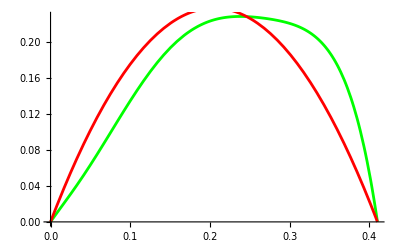

```mathematica
Show[Plot[v[y],{y,0,h}, PlotStyle->Green],Plot[vflat[y],{y,0,h}, PlotStyle->Red]]
```

```mathematica
t=Import["~/Desktop/v_L.csv"]
```

```mathematica
t=Table[{t[[i,5]],t[[i,1]]},{i,1,Length[t]}]
```

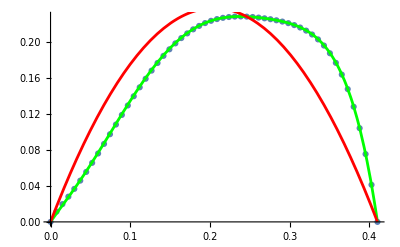

```mathematica
Show[ListPlot[t],Plot[v[y],{y,0,h}, PlotStyle->Green],Plot[vflat[y],{y,0,h}, PlotStyle->Red]]
```